```mathematica
SetDirectory["C:\\Users\\John\\SkyDrive\\Documents\\Task\\NegPolaron"]
```

C:\Users\John\SkyDrive\Documents\Task\NegPolaron

## Introduction of representation

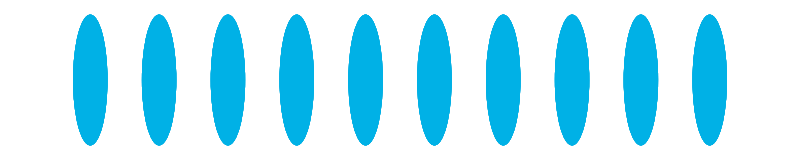

```mathematica
f1=Graphics[Array[{Hue[#2/3.9,1,0.9,0.6],Disk[{#1,0},10]}&,{10,10},{{40,400.},{6.,6.}}],ImageSize->800,Axes->False]
```

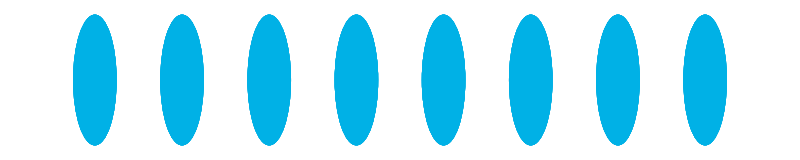

```mathematica
f1=Graphics[Array[{Hue[#2/3.9,1,0.9,0.6],Disk[{#1,0},10]}&,{8,10},{{120,400.},{6.,6.}}],ImageSize->800,Axes->False]
```

```mathematica
ls=Transpose[{Range[200],phiToU[config[[10]]]}][[1;;200]];
```

```mathematica
Riffle[Array[1&,5],Array[-1&,5]]
```

{1,-1,1,-1,1,-1,1,-1,1,-1}

```mathematica
maxd=.12;
```

```mathematica
ls=Transpose[{Array[#1&,8,{120,400}],Riffle[Array[3&,4],Array[-3&,4]]}]
```

{{120,3},{160,-3},{200,3},{240,-3},{280,3},{320,-3},{360,3},{400,-3}}

```mathematica
Epilog->(Inset[Style[#1,Bold,16],#2]&@@@Transpose[{Array[#1&,5,Reverse@{-0.0036800,0.082500}],Array[{.3,#1}&,5,{10.1,11.}]}])
```

Epilog→{Inset[0.0825,{0.3,10.1}],Inset[0.060955,{0.3,10.325}],Inset[0.03941,{0.3,10.55}],Inset[0.017865,{0.3,10.775}],Inset[-0.00368,{0.3,11.}]}

```mathematica
legd=Graphics[Array[{Hue[#1],Opacity[.8],Rectangle[{0,#1+10.},{.2,#1+10.01}]}&,400,{0.1,1.}],Axes->False,Epilog->(Inset[Style[#1,Bold,16],#2]&@@@Transpose[{Array[#1&,5,{-2,2}],Array[{.3,#1}&,5,{10.1,11.}]}]),PlotRange->{{-.12,.7},{10.,11.1}}];
```

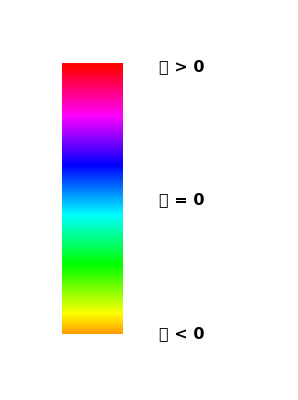

```mathematica
legdt=Graphics[Array[{Hue[#1],Opacity[.8],Rectangle[{0,#1+10.},{.2,#1+10.01}]}&,400,{0.1,1.}],Axes->False,Epilog->(Inset[Style[#1,Bold,16],#2]&@@@Transpose[{Style[#1,Bold,16]&/@{"𝓊 < 0","𝓊 = 0", "𝓊 > 0"},Array[{.4,#1}&,3,{10.1,11.}]}]),PlotRange->{{-.12,.7},{10.,11.1}}]
```

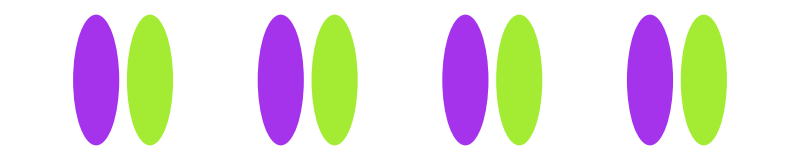

```mathematica
f2=Graphics[{Hue[#2/3.9,1,0.9,0.8],Disk[{#1+#2/0.36,-70},10]}&@@@ls,ImageSize->800]
```

```mathematica
l1=Graphics[{Dashed,Thick,Line[{{200,-0},{200,-40}}]}]
```

-Graphics-

```mathematica
l2=Graphics[{Dashed,Thick,Line[{{200+3/0.36,-70},{200+3/0.36,-40}}]}]
```

-Graphics-

```mathematica
tu=Graphics[Text[Style["𝓊",Bold,20],{200+0.5*3/0.36,-40+2}]];
```

```mathematica
ta=Graphics[Text[Style["(a)",Bold,20],{90,-0}]];
```

```mathematica
tb=Graphics[Text[Style["(b)",Bold,20],{90,-70}]];
```

```mathematica
ap=Graphics[{Dashed,Thick,Arrow[{{120,20},{120+40,20}}]}];
```

```mathematica
tua=Graphics[Text[Style["𝓊 > 0",Bold,20],{120+40+15,20}]];
```

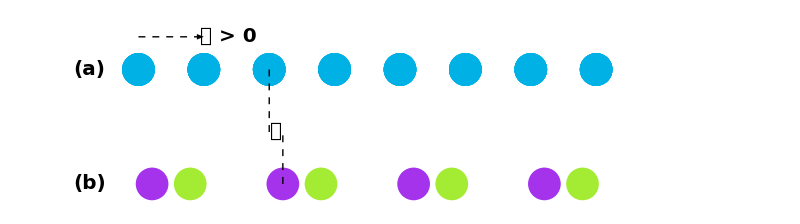

```mathematica
fd=Show[{f1,f2,l1,l2,tu,ta,tb,ap,tua},Epilog->Inset[legdt,{455,-37},Automatic,70],PlotRange->{{80,480},{-82,30}},Axes->False]
```

```mathematica
Export["latdiaintr.png",fd,ImageResolution->600]
```

latdiaintr.png

## applied to

```mathematica
config=Flatten@Import["dphi.dat"];
```

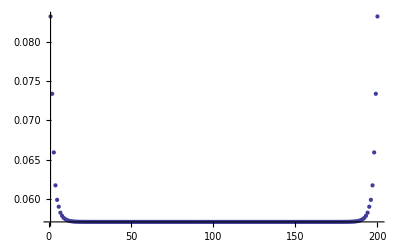

```mathematica
ListPlot[config,PlotRange->All]
```

```mathematica
Dimensions[config]
```

{200}

```mathematica
config2=Flatten@Import["adphi.dat"];
```

```mathematica
config2[[100]]
```

0.0366214

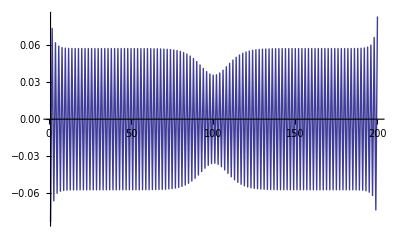

```mathematica
ListPlot[phiToU[config2[[1;;200]]],PlotRange->All,Joined->True]
```

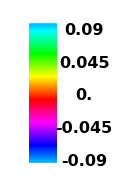

```mathematica
legdintro=Graphics[Array[{Hue[#1],Opacity[.8],Rectangle[{0,#1+10.},{.2,#1+10.01}]}&,400,{-0.46,0.54}],Axes->False,Epilog->(Inset[Style[#1,Bold,16],#2]&@@@Transpose[{Array[#1&,5,{-0.09,0.09}],Array[{.4,#1}&,5,{9.55,10.5}]}]),PlotRange->{{-.12,.7},{9.5,10.6}}]
```

```mathematica
Graphics[Array[{Hue[#1],Opacity[.8],Rectangle[{0,#1+10.},{.2,#1+10.01}]}&,400,{0.1,1.}],Axes->False,Epilog->(Inset[Style[#1,Bold,16],#2]&@@@Transpose[{Style[#1,Bold,16]&/@{"𝓊 < 0","𝓊 = 0", "𝓊 > 0"},Array[{.4,#1}&,3,{10.1,11.}]}]),PlotRange->{{-.12,.7},{10.,11.1}}]
```

```mathematica
lss=Transpose[{Range[61],phiToU[config[[70;;130]]]}];
```

```mathematica
lss21=Transpose[{Array[#1&,61,1],phiToU[config2[[70;;130]]]}];
```

```mathematica
lss2=Transpose[{Array[#1&,61,{11.,51}],phiToU[config2[[70;;130]]]}];
```

```mathematica
Graphics[{Hue[5*#2],Disk[{#1+#2+65,5*Sin[#1/10.]},.4]}&@@@lss,ImageSize->1400,Axes->False]
```

```mathematica
f1=Graphics[{Hue[5*#2],Disk[{#1+#2+65,5*Sin[#1/10.]},.4]}&@@@lss,ImageSize->1400,Axes->False]
```

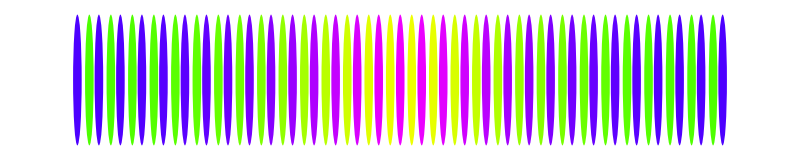

```mathematica
Graphics[{Hue[5*#2],Opacity[1],Disk[{#1+#2+65,0},.4]}&@@@lss21,ImageSize->800,Axes->False]
```

```mathematica
f1=Graphics[{Hue[5*#2],Opacity[1],Disk[{#1+#2+65,0},.4]}&@@@lss21,ImageSize->800,Axes->False]
```

-Graphics-

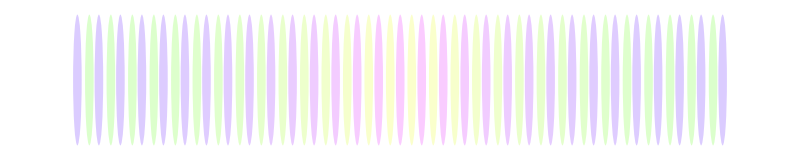

```mathematica
f11=Graphics[{Hue[5*#2],Opacity[0.2],Disk[{#1+#2+65,0},.4]}&@@@lss21,ImageSize->800,Axes->False]
```

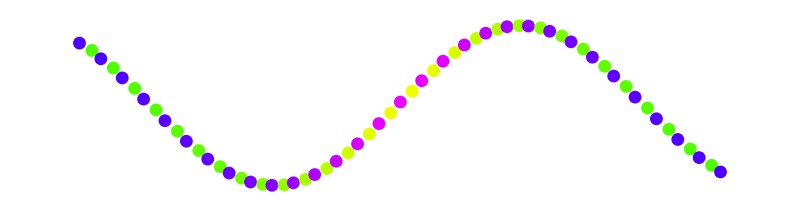

```mathematica
f2=Graphics[{Hue[5*#2],Disk[{#1+#2+65,5*Sin[(1#1)/4.9]-8+8},.4]}&@@@lss2,ImageSize->800,Axes->False]
```

```mathematica
pcir=Graphics[{Dashed,Thickness[0.01],Circle[]},ImageSize->80]
```

-Graphics-

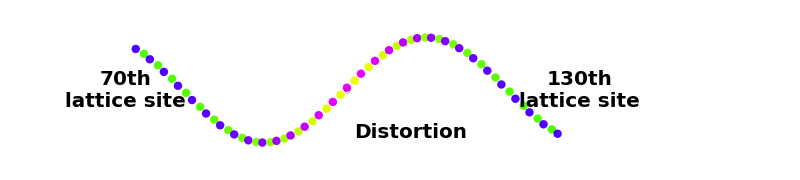

```mathematica
ppa1=Show[{f2},PlotRange->{{70,132},{-7,7}},Epilog->{Inset[legdintro,{126.8,-0},Automatic,10],Inset[Style["70th\nlattice site",Bold,20],{75,-0},Automatic,10],Inset[Style["130th\nlattice site",Bold,20],{118,-0},Automatic,10],Inset[Style["Distortion",Bold,20],{102,-4},Automatic,10],Inset[pcir,{96,-0},Automatic,14]},Axes->False,ImageSize->800]
```

```mathematica
Export["fo3.png",ppa1,ImageResolution->600]
```

fo3.png

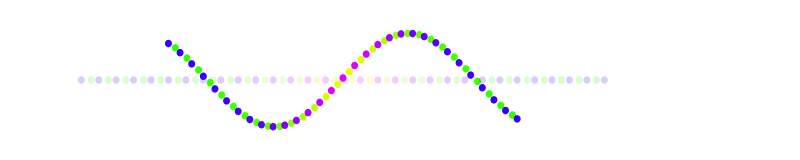

```mathematica
ppa2=Show[{f2,f11},PlotRange->{{65,140},{-7,7}},Epilog->{Inset[legdintro,{132.8,-0},Automatic,10],Inset[,{132.8,-0},Automatic,10]},Axes->False,ImageSize->800]
```

```mathematica
Export["fo4.png",ppa2,ImageResolution->600]
```

fo4.png

```mathematica
Manipulate[Graphics[{Hue[5*#2],Disk[{#1+#2+65,5*Sin[(k#1)/4.9]-8+8},.4]}&@@@lss2,ImageSize->800,Axes->False],{k,0.1,1,0.05}]
```

```mathematica
Manipulate[Graphics[{Hue[5*#2],Disk[{#1+#2/k,0},.4]}&@@@lss2,ImageSize->1400],{k,0.01,0.9,0.01}]
```

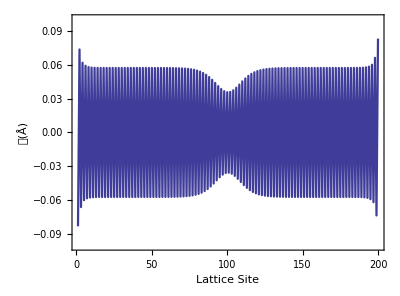

```mathematica
fa3=ListPlot[phiToU[config2[[1;;200]]],PlotStyle->Directive[Thickness[0.004]],PlotRange->{All,{-0.1,0.1}},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Thickness[0.006],FontSize->20],ImageSize->400,FrameLabel->(Style[#1,Bold,20]&/@{"Lattice Site","𝓊(Å)"}),AspectRatio->0.74]
```

```mathematica
Export["fo5.png",fa3,ImageResolution->600]
```

fo5.png